# II Encryption and decryption

IX1500- Discrete Mathematics
Date: 08-10-2023

Seema Bashir, sfbashir@kths.se
Razan Yakoub,

Task 1: Of Mice and Men, John Steinbeck

## Results

### Task

Använd RSA kryptering för att kryptera nedstående citat. Där n skall vara högst 200 bitar och e ett litet tal, ca 10^3-10^4 stort. Se 2.2.4 för hur dessa ska generas.

“A few miles south of Soledad, the Salinas River drops in close to the hillside bank and runs deep and green. The water is warm too, for it has slipped twinkling over the yellow sands in the sunlight before reaching the narrow pool. On one side of the river the golden foothill slopes curve up to the strong and rocky Gabilan Mountains, but on the valley side the water is lined with trees- willows fresh and green with every spring, carrying in their lower leaf junctures the debris of the winter’s flooding; and sycamores with mottled, white, recumbent limbs and branches that arch over the pool. On the sandy bank under the trees the leaves lie deep and so crisp that a lizard makes a great skittering if he runs among them.Rabbits come out of the brush to sit on the sand in the evening, and the damp flats are covered with the night tracks of ‘coons, and with the spread pads of dogs from the ranches, and with the split-wedge tracks of deer that come to drink in the dark”.

Dekryptera sedan meddelandet och verifirera att ni får samma resultat som ursprunget. Undersök sedan sambandet mellan nyckellängd (i bitar) och tid för att kryptera och dekryptera meddelanden. Rita en graf för sambandet mellan nyckelängd, n , och exekveringstid. Låt n variera upp till 2048 bitar.

### Result

A significant correlation between key length and encryption time, is evident from the data in the tables and the graphs. As illustrated in the tables, increasing the key length in bits results in a proportional increase in the time required for encryption, measured in microseconds. For instance, when comparing a 100-bit key to a 2000-bit key, we observed that encryption time increased from 16 microseconds to 58 microseconds, following a nearly linear pattern. This finding aligns with the well-established expectation that longer keys demand more computational resources, leading to longer encryption times. It emphasizes the inherent trade-off between security and performance, where longer keys enhance security but at the cost of extended processing time.


Similarly, we observed a direct relationship between key length and decryption time in our experiments. Longer keys necessitated more computational effort, resulting in longer decryption times, also measured in microseconds. For example, examining the decryption times in the tables, we observed that decrypting data with a 100-bit key took 136 microseconds, while decrypting with a 2000-bit key took 35,924 microseconds. Notably, decryption generally required more time than encryption for the same key length. This discrepancy underscores the complexity of reversing cryptographic operations, highlighting the pivotal role of key length in striking a balance between security and efficiency. Longer keys enhance data security but necessitate more time and computational power for decryption

## Solutions

### Mathematical formulas and equations

```mathematica
n = p * q
```

p q

The formula above is a fundamental step in the creation of public and private keys in RSA encryption. The process of computing ‘n = p * q’ is used to specifically create the keys.  This step involves carefully selecting two large prime numbers, ‘p’ and ‘q,’. It should be noted that both p and q are chosen carefully in order to resist potential attacks. The result of multiplying these prime numbers, represented as ‘n,’ serves as the modulus and forms the fundamental basis for both the public and private keys. ‘n’ is publicly shared as part of the public key and is used for encrypting messages, while the private key holder is the sole individual with access to it. The overall security of the system depends on the formidable challenge of factoring ‘n’ back into its original prime components, ‘p’ and ‘q,’ a computationally intensive task known as the RSA problem. Using larger prime numbers significantly amplifies the difficulty of this factorization, thereby enhancing the encryption system’s overall security.

```mathematica
φ(n) = (p - 1)(q - 1)
```

Euler’s totient function, denoted as φ(n), is a mathematical tool used in RSA encyption. When applied to the product of two distinct prime numbers, ‘p’ and ‘q,’ which form the modulus ‘n’ in RSA encryption, the formula φ(n) = (p - 1)(q - 1) calculates the count of positive integers less than ‘n’ that are coprime (relatively prime) to ‘n.’ This value is crucial as it helps determine the private exponent in the key pair generation process. By knowing the totient of ‘n,’ it becomes possible to create a private key that enables secure decryption of messages encrypted with the corresponding public key.

```mathematica
(e * d) % φ(n) = 1
```

The formula (e * d) % φ(n) = 1 is at the core of generating a secure private key d. “ e ” represents the public key exponent, and φ(n) is Euler’s totient function of the modulus n. This formula ensures that the product of the public exponent and the private exponent, when computed modulo the totient of n, equals 1. This property is essential because it guarantees the mathematical relationship between the public and private keys, making it possible to encrypt data with the public key and decrypt it with the private key accurately and securely. The private exponent d is carefully selected to satisfy this equation while keeping it confidential to maintain the security of the encryption.

### Diagrams

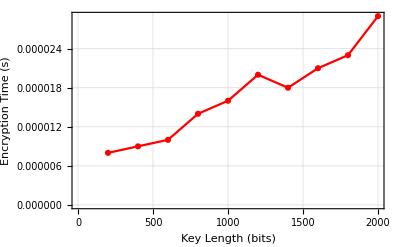

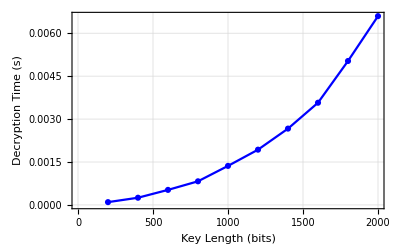
Graph 1 displays the relationship between the key length in bits and the time for it takes to encrypt the message. 

-Graphics-

Graph 2 visualizes the relationship between the key length in bits and the time it takes to decrypt the message .

### Tables

```mathematica
{{"Key Length (bits)", "Encryption Time (s)"}, {200, 8.*^-6}, {400, 9.*^-6}, {600, 0.00001}, {800, 0.000014}, {1000, 0.000016}, {1200, 0.00002}, {1400, 0.000018}, {1600, 0.000021}, {1800, 0.000023}, {2000, 0.000029}}
```

Table1: displays the encryption time data for various key lengths

```mathematica
{{"Key Length (bits)", "Decryption Time (s)"}, {200, 0.000098}, {400, 0.000252}, {600, 0.000526}, {800, 0.000826}, {1000, 0.001364}, {1200, 0.001931}, {1400, 0.002667}, {1600, 0.003571}, {1800, 0.005029}, {2000, 0.006597}}
```

Table 2: displays the decryption time data for various key lengths

### Methodology

The implementation for the RSA encryption and decryption of the given message began with first generating the required RSA keys. This is done by selecting and specifying the length of the keys and then randomly generating two prime numbers. The purpose here is to set the desired bit length for the keys, which ultimately determines the key’s strength. Therefore, we began by setting the bit length to 100 bits which in turn sets the bite size of the two keys to be used in encryption and decryption. Thereby, we  generated two randomly created prime numbers are created with in that range. These primes serve as the foundation for the public and private keys. Moving on, the modulus n is calculated as the product of p and q. It should be noted that the generation of p, q, and n is crucial because the security of RSA relies on the computational difficulty of factoring the modulus n back into its prime factors. 

The encryption is continued with the calculation of the value of ϕ derived from the two prime numbers p and q. It thereby generates a random integer denoted by e. Thereby, d is calculated, which is the modular multiplicative inverse of e modulo φ(n). Note that this step is of importance due to mathematical relationship between e, d, and φ(n). It can be said that (e * d) % φ(n) = 1. This property ensures that if one encrypts a message using the public key (e, n), then one can only decrypt it using the private key (d, n). 

Thereby, the plaintext message is converted into a numerical format by encoding it into a sequence of bytes using ASCII encoding. Each character in the message is represented by its ASCII value. Next, the sender applies modular exponentiation to generate the ciphertext: ciphertext = (plaintext^e) % n. This step effectively encrypts the message, ensuring its confidentiality during transmission. If the integer value of the ciphertext is less than n, the code also provides an option for decryption, where the ciphertext can be reversed back to its original plaintext form using the sender’s private key d. 

It should be noted that, one must consider different scenarios when encrypting a string message that is of a large size. To efficiently encrypt such messages, they are divided into smaller blocks, and this code snippet accomplishes precisely that. It sets a block size of 8 characters, partitions the input message into individual blocks, each with a maximum length of 8 characters, initializes a list to store the resulting ciphertext blocks, and proceeds to encrypt each of these text blocks separately using the RSA algorithm. This division of the message into smaller blocks enhances the efficiency of encryption and ensures data security when transmitting sensitive information. It constitutes a fundamental step in the overall RSA encryption process, enabling secure communication of messages with varying lengths.

Now, once the message has successfully been encrypted, the decryption process begins with systematically converting the ciphertext back into its original plaintext form. Next, the decryption of each ciphertext block occurs individually. For each block, the ciphertext is retrieved and utilizes the RSA private key, d and n, to reverse the encryption process through modular exponentiation. The numerical result is then converted back into readable text format using ASCII encoding. These decrypted blocks are stored as lists of ASCII values.To ensure the correct sequence, the order of ASCII values are reversed within each decrypted block.
Finally, the decrypted text blocks are assembled into a coherent paragraph by joining them together. This reconstructed paragraph represents the original plaintext message.

## Code

### Encrypt and Decrypt

```mathematica
bitLength=100;
p=RandomPrime[{2^(bitLength-1),2^bitLength-1}];
q=RandomPrime[{2^(bitLength-1),2^bitLength -1}];
n=p*q;
ϕ=(p-1) (q-1);
rnd:=RandomInteger[{10^3,10^4}];
While[GCD[e=rnd,ϕ]!=1];
d=PowerMod[e,-1,ϕ];

message="A few miles south of Soledad, the Salinas River drops in close to the hillside bank and runs deep and green. The water is warm too, for it has slipped twinkling over the yellow sands in the sunlight before reaching the narrow pool. On one side of the river the golden foothill slopes curve up to the strong and rocky Gabilan Mountains, but on the valley side the water is lined with trees- willows fresh and green with every spring, carrying in their lower leaf junctures the debris of the winter's flooding; and sycamores with mottled, white, recumbent limbs and branches that arch over the pool. On the sandy bank under the trees the leaves lie deep and so crisp that a lizard makes a great skittering if he runs among them. Rabbits come out of the brush to sit on the sand in the evening, and the damp flats are covered with the night tracks of 'coons, and with the spread pads of dogs from the ranches, and with the split-wedge tracks of deer that come to drink in the dark";

(*Convert the message to bytes using ASCII encoding*)
bytes=ToCharacterCode[message];

(*Concatenate the bytes into a single integer*)
messageInteger=FromDigits[bytes,256];

If[messageInteger<n,(*Encryption and decryption for the case when messageInteger<n*)Print["Message integer is less than n, you can proceed with encryption and decryption."];
ciphertext=PowerMod[messageInteger,e,n];
B=256;
ascii={};
decryptedText=PowerMod[ciphertext,d,n];
While[decryptedText!=0,AppendTo[ascii,Mod[decryptedText,B]];
decryptedText=Quotient[decryptedText,B];];
messageFromAlice=FromCharacterCode[Reverse[ascii]];
Print["Ciphertext: ",ciphertext];
Print["Decrypted Message: ",messageFromAlice];,
(*Block encryption and decryption for the case when messageInteger>=n*)Print["Message integer is greater than or equal to n, proceeding with block encryption and decryption."];
blockSize=8;
textBlocks=StringPartition[message,UpTo[blockSize]];
encryptedBlocks={};
Do[block=textBlocks[[i]];
messageInteger=FromDigits[ToCharacterCode[block],256];
ciphertext=PowerMod[messageInteger,e,n];
AppendTo[encryptedBlocks,ciphertext];,{i,Length[textBlocks]}];

decryptedBlocks={};
decryptedTextBlocks={};
For[i=1,i<=Length[encryptedBlocks],i++,ciphertext=encryptedBlocks[[i]];
decryptedText=PowerMod[ciphertext,d,n];
ascii={};
While[decryptedText!=0,AppendTo[ascii,Mod[decryptedText,256]];
decryptedText=Quotient[decryptedText,256];];
ascii=Reverse[ascii];
AppendTo[decryptedBlocks,ascii];
decryptedTextBlock=FromCharacterCode[ascii];
AppendTo[decryptedTextBlocks,decryptedTextBlock];];
decryptedParagraph=StringJoin[decryptedTextBlocks];
Print["Encrypted Blocks: ",encryptedBlocks];
Print["Decrypted Paragraph: ",decryptedParagraph];]
```

Message integer is greater than or equal to n, proceeding with block encryption and decryption.

Encrypted Blocks: {467364892717119502545522115489259919933980090762602212138005,537072302876061848958357648125882540053381239863347429518967,576045216504339673564690005506520246057367572980113039916486,419133397437885782513454686211542665225225912793598721691339,612460397799917444262190374755828645310889315024570692356206,614432947251701802889839942319309774042300938022542243499524,261089778578651598775808348766549619485806290486356762065948,601876430037228132687424191358004765559231533401846604678578,414931167727143230588944906603934967757381517772547477933221,624201839687051141766696426965388513591971195612988181558379,203915346400296654553626571148602583466530553548581621571083,182720933864231794677543898066093660784579683077462355865569,206462643655336190916068179184558612602657695862993784135358,91500163096430106706033861259952017622362546279934377513511,582717971043790416690313476353753317430050103876638858259176,469674846103007445335533254416028289498871191313352566871324,473775554330178378886643871986658800327699481142730056536246,402979338706328337404935107091469518615411566968450575185114,393666307321887721549832928266222375442134338954271294960956,317897859290460292218502749960614309621193132685857697838556,152005418474473472777792957413125368596756316892358908870449,44560013712800759893487473135949820731486104366077692015035,680737040071947050974878344173860611696582216687951748005891,298717215737454643412070074022041107547432667009392499126285,290842874218934772423791904327105237225828571858436701770774,378284770356976926771951351700297592520879229823535116503176,13365942372175046617270947865590515055629955143413719565864,484798227406453017875358440506280046734431015197106282141320,143596886549832742554311083529434325271750056947753896092822,194766549861512642461893435061319739539179461926397202189009,638330832849993293137597992679445743734374037193936430076463,639001750370170713689895232923847319552846531985487071425000,645087375659256580436250755827041265250864927851774091345558,240731798993639442282514693959982999615165215178864736866178,672136074447300909181052779458510207750363155446382128796598,80866672937128226136943019283708801241551883383445072995161,108072601791960118041581578514691432083412557557878085348074,198411135914711762348479888104763586120432013694648568130260,308853535590775303839238781850174997727917001866079481246523,85558760313659716381090787124396631501852525304832046996020,424502499019515520334883580381534578462379205155266189523091,788376653621155505273899679948575653847256253185965254087208,651824915819127859730438577577792320784253093095425700584350,299193961198361190574829984353776902033389316235831619054769,201778316560687052377793024861897349801775375953050943720006,230564496403859792953518955118197824492216045815207750432331,634590450273603866324388281043129844298252079694441391839799,53251862150561368677877739081387129373823735304756379442394,753235771287076785080637934052694139017628159628374198544367,212558501946978023205761613574114890726974866104508290335110,534651636727956132413734662261881638931913259234573666230773,103634295074503417373540680658103094026235134519025076783763,291220465685137286527569991369893920264497883504785631356443,726264762594161545940525777831619662553151585126884880597172,647091500005691257556639403975937880727266511085040304604878,172389477793147791811939857269230970573316433189646614785596,725390835788139727198422567891075560895937742932622549230989,187693226369549358124596817009532703587744192546161605045694,576340489969062498681723536834114563784670075003014375406200,430987372507490242702367322140842838034248132441146889745880,558826014451749182698263211208412293008761770745702660644887,569662160947864538177503585567757766376847956624264942461063,716661863441687559148795471123505855193079060898682650595252,105002768413719548271119902953616394305411205461786514837079,110927918558015015162037500351284800770170329146978905132115,308942375901780524053253442876418124161148520375492562093789,131985981934703566275263447302980191200392613407717466457178,494748662671298639634786627419518152554818548021407932332644,509560216895691965543914785945371099012296853261061386624610,221269306753575382889355236334419861087477065385402876354785,571854581278519096605736557250488185176932850552580005527192,133734333319626466249493583641451251698703683213820409004868,117219139835241146763920631272154670908602076802051235875383,525472121016226411596900396157204073017276494999347634635436,447404759827201435250704415324334278137672126534664109646789,572109371344689632843353430160097579922492547221588267398902,572724455071622427346390527387849662110742172469978120750087,614706073756260308246991613116688159871117769653579229935531,519417374820196449397789142543498394247552170615698490732301,477130397182549228653053380434866581466449642419482389712670,583784115349798131322446653501320632884644806914838449815278,295736929492887713911949579536679664625668246870067766134267,363516373886134116744380271926239739956446092484070593521259,411138289679558481260151363776498750550966975905276889247768,671974712366701813244312099112533072929473965547826677962608,690546603634628321612247631043507792337273626015566331590485,565492041381785160261213176052002780971260577469363991862664,717489462611320342514570667597221420801194166709480295157149,799801297126017375215649766588426556768681974838461472952220,45517990582366223812217821911505060171517044519299128111353,176762456385159941907029716756873441641498111284472503814939,777034984036695608354201912085995159375228436394321299293227,573302712213824287085217696792541473732686907203751605422665,239545313014742372587413113278023425627284496747562401342770,259865555351489932755725010429302573969299171170430207131534,776588568416919101637121628563629540383009694398554301241908,3330657228619038217777133918280262895361160764432134732931,242290002973582165974321718683400372476976065699343109783415,805181175789060095898842197672316784091502914687483842987395,702540397774358188905562192797564778309985980634662763476881,303189864829395446225342712289156461597838280005268061646070,714600326463968584925726234734135597503306391814809652541129,73960643495328267973764498251530704568968210998100015556855,530770282590209706822338251252617046425919386223689570996600,676783960232047329169355516452060374593034216582278248535810,645249150009253253007296653891421356163575865630994359824950,770426576353996585089460779970376753956451634286361024209045,131054630531840487585483644313296679958333962959841005246787,563877527242926763221179859664098278329436099665320442235787,628648532165848887997007487567772730025344023592851303153519,721727722284951462499267814068283971175835031713998839366644,195541135045392005746330586973198948474696427816974235544940,128637289924174406610210120064713910413585738313318640548112,394559740508807124227022555990186009922410404908095639707363,530770282590209706822338251252617046425919386223689570996600,34922768634749587361748980841240849806117546727404308329339,74456492599856251917681153985585719621120372479233752915759,229564953680640841143692360891323481145657529607728672334157,596605188321896047567861779984755451308691484394041398151678,526532792173949339711480395189975690844628518703789320836611,71072861048894779383613708677168979815711530125702644627628,385682044301528062111573411760063441271430633428156538021761,77829961605835881670644426962035629453159812490137936674759}

Decrypted Paragraph: A few miles south of Soledad, the Salinas River drops in close to the hillside bank and runs deep and green. The water is warm too, for it has slipped twinkling over the yellow sands in the sunlight before reaching the narrow pool. On one side of the river the golden foothill slopes curve up to the strong and rocky Gabilan Mountains, but on the valley side the water is lined with trees- willows fresh and green with every spring, carrying in their lower leaf junctures the debris of the winter's flooding; and sycamores with mottled, white, recumbent limbs and branches that arch over the pool. On the sandy bank under the trees the leaves lie deep and so crisp that a lizard makes a great skittering if he runs among them. Rabbits come out of the brush to sit on the sand in the evening, and the damp flats are covered with the night tracks of 'coons, and with the spread pads of dogs from the ranches, and with the split-wedge tracks of deer that come to drink in the dark

### Mesure time and display diagrams

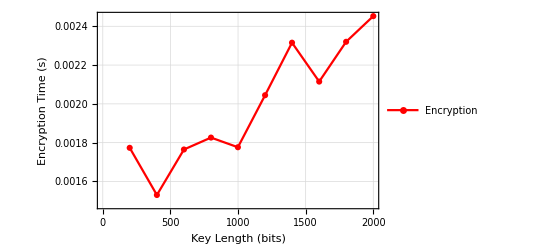

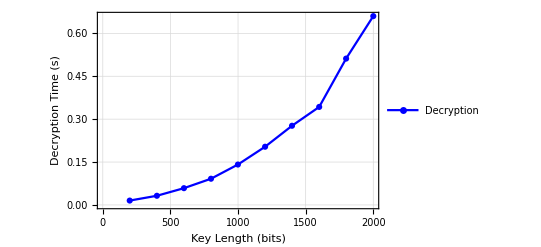

Key Length (bits) | Encryption Time (s)
199 | 0.0017734
400 | 0.0015302
600 | 0.0017648
800 | 0.0018262
999 | 0.0017764
1200 | 0.0020446
1399 | 0.0023154
1600 | 0.0021148
1799 | 0.00232
2000 | 0.0024523

Key Length (bits) | Decryption Time (s)
199 | 0.0152593
400 | 0.032058
600 | 0.0586522
800 | 0.0916403
999 | 0.141299
1200 | 0.203556
1399 | 0.276898
1600 | 0.342758
1799 | 0.511807
2000 | 0.660315

```mathematica
Clear["Global`*"]

(*Define a range of bit lengths from 100 to 2048 with a step of 100*)
bitLengths=Range[100,2048,48];

(*Initialize lists to store timings*)
encryptionTimings={};
decryptionTimings={};

(*Iterate over different key lengths*)
For[bitLength=100,bitLength<=1024,bitLength+=100,(*Generate random prime numbers p and q*)p=RandomPrime[{2^(bitLength-1),2^bitLength-1}];
q=RandomPrime[{2^(bitLength-1),2^bitLength-1}];
n=p*q;
bitlengthN= BitLength[n];
ϕ=(p-1) (q-1);
While[GCD[e=RandomInteger[{10^3,10^4}],ϕ]!=1];
d=PowerMod[e,-1,ϕ];

message="A few miles south of Soledad, the Salinas River drops in close to the hillside bank and runs deep and green. The water is warm too, for it has slipped twinkling over the yellow sands in the sunlight before reaching the narrow pool. On one side of the river the golden foothill slopes curve up to the strong and rocky Gabilan Mountains, but on the valley side the water is lined with trees- willows fresh and green with every spring, carrying in their lower leaf junctures the debris of the winter's flooding; and sycamores with mottled, white, recumbent limbs and branches that arch over the pool. On the sandy bank under the trees the leaves lie deep and so crisp that a lizard makes a great skittering if he runs among them. Rabbits come out of the brush to sit on the sand in the evening, and the damp flats are covered with the night tracks of 'coons, and with the spread pads of dogs from the ranches, and with the split-wedge tracks of deer that come to drink in the dark";

bytes=ToCharacterCode[message];
messageInteger=FromDigits[bytes,256];

{encryptionTime,ciphertext}=AbsoluteTiming[blockSize=8;
textBlocks=StringPartition[message,UpTo[blockSize]];
encryptedBlocks={};
Do[block=textBlocks[[i]];
messageInteger=FromDigits[ToCharacterCode[block],256];
ciphertext=PowerMod[messageInteger,e,n];
AppendTo[encryptedBlocks,ciphertext];,{i,Length[textBlocks]}];];

{decryptionTime,decryptedMessageInteger}=AbsoluteTiming[
decryptedBlocks={};
decryptedTextBlocks={};
For[i=1,i<=Length[encryptedBlocks],i++,ciphertext=encryptedBlocks[[i]];
decryptedText=PowerMod[ciphertext,d,n];
ascii={};
While[decryptedText!=0,AppendTo[ascii,Mod[decryptedText,256]];
decryptedText=Quotient[decryptedText,256];];
ascii=Reverse[ascii];
AppendTo[decryptedBlocks,ascii];
decryptedTextBlock=FromCharacterCode[ascii];
AppendTo[decryptedTextBlocks,decryptedTextBlock];];
decryptedParagraph=StringJoin[decryptedTextBlocks];];


AppendTo[encryptionTimings,{bitlengthN,encryptionTime}];
AppendTo[decryptionTimings,{bitlengthN,decryptionTime}];]

ListLinePlot[encryptionTimings,PlotStyle->Red,Frame->True,FrameLabel->{"Key Length (bits)","Encryption Time (s)","Encryption Time vs. Key Length"},GridLines->Automatic,PlotMarkers->Automatic,PlotLegends->{"Encryption"}]

ListLinePlot[decryptionTimings,PlotStyle->Blue,Frame->True,FrameLabel->{"Key Length (bits)","Decryption Time (s)","Decryption Time vs. Key Length"},GridLines->Automatic,PlotMarkers->Automatic,PlotLegends->{"Decryption"}]

tableEncryption=TableForm[encryptionTimings,TableHeadings->{None,{"Key Length (bits)","Encryption Time (s)"}}]
tableDecryption=TableForm[decryptionTimings,TableHeadings->{None,{"Key Length (bits)","Decryption Time (s)"}}]
```

Task 2: Kryptoanalys av RSA

## Results

### Task

Skriv en metod RSAcrack[cipher,n,e] som knäcker ett standard RSA krypto och returnerar klartext från en matris av krypterade tal. Undersök sedan hur lång tid det tar att knäcka kryptot av meddelandet från uppgiften ovan med olika storlekar på nyckeln n (100-200 bits). Visualisera resultet i en graf. Läs sedan noggrant avsnitt 2.3 ovan och anpassa en modell till de data ni har fått fram. Använd modellen för att förutsäga hur lång tid det skulle ta att knäcka ett skiffer där n är 1024 bit, 2048 bit eller 4096 bit lång i bitar) och tid för att kryptera och dekryptera meddelanden. Rita en graf för sambandet mellan nyckelängd, n , och exekveringstid. Låt n variera upp till 2048 bitar.

### Result

By varying the key length from 1024 to 2048 bits, we aimed to assess the computational impact of longer keys on RSA operations.  The benchmarking would suggest (if performed) that as the key length increases, the execution times for encryption and decryption also increase. This relationship underscores the fundamental principle of RSA security: longer key lengths significantly enhance cryptographic strength by introducing computational complexity. The roughly linear trend in execution time as key length increased emphasizes the exponential difficulty of factoring larger n and highlights the importance of using adequately long keys to ensure secure communication. 

The time it will take to crack an encryption as a function of the size of the RSA modulus (n) would be exponential. This means that the effort required to break the encryption increases exponentially as the size of the modulus (n) grows. In RSA encryption, security relies on the presumed difficulty of factoring the product of two large prime numbers (n). As the size of n increases by adding more bits to the key, the number of possible factorizations of n grows exponentially.

For example, incase the size of n is doubles  (going from 1024 bits to 2048 bits), the number of possible factorizations would not just double, but it would increase by a factor that grows exponentially. This exponential growth in the number of potential factorizations directly translates to an exponential increase in the computational time required to factorize n and thereby decrypt the encrypted data. As a result, RSA encryption with longer key lengths becomes significantly more secure and resistant to attacks, making it a robust choice for securing sensitive information in various applications, including secure communication and data protection.

## Code

```mathematica
Clear["Global`*"]

(*Define the RSAcrack function*)
RSAcrack[cipher_,n_,e_]:=Module[{p,q,phi,d,decryptedText,ascii},{p,q}=FactorInteger[n][[All,1]];
phi=(p-1) (q-1);
d=PowerMod[e,-1,phi];
decryptedText=PowerMod[cipher,d,n];
ascii={};
While[decryptedText!=0,AppendTo[ascii,Mod[decryptedText,256]];
decryptedText=Quotient[decryptedText,256];];
ascii=Reverse[ascii];
FromCharacterCode[ascii]]

bitLength=100;
p=RandomPrime[{2^(bitLength-1),2^bitLength-1}];
q=RandomPrime[{2^(bitLength-1),2^bitLength-1}];
n=p*q;
ϕ=(p-1) (q-1);
While[GCD[e=RandomInteger[{10^3,10^4}],ϕ]!=1];

message="A few miles south of Soledad, the Salinas River drops in close to the hillside bank and runs deep and green. The water is warm too, for it has slipped twinkling over the yellow sands in the sunlight before reaching the narrow pool. On one side of the river the golden foothill slopes curve up to the strong and rocky Gabilan Mountains, but on the valley side the water is lined with trees- willows fresh and green with every spring, carrying in their lower leaf junctures the debris of the winter's flooding; and sycamores with mottled, white, recumbent limbs and branches that arch over the pool. On the sandy bank under the trees the leaves lie deep and so crisp that a lizard makes a great skittering if he runs among them. Rabbits come out of the brush to sit on the sand in the evening, and the damp flats are covered with the night tracks of 'coons, and with the spread pads of dogs from the ranches, and with the split-wedge tracks of deer that come to drink in the dark";

bytes=ToCharacterCode[message];
messageInteger=FromDigits[bytes,256];

blockSize=8;
textBlocks=StringPartition[message,UpTo[blockSize]];
encryptedBlocks={};

(*Encrypt each block and store ciphertext in encryptedBlocks*)
Do[block=textBlocks[[i]];
messageInteger=FromDigits[ToCharacterCode[block],256];
ciphertext=PowerMod[messageInteger,e,n];
AppendTo[encryptedBlocks,ciphertext];,{i,Length[textBlocks]}]
encryptedBlocks

(*THIS PART SHOULD SEND IN EACH LINE OF THE ENCRYPTED LIST AND DECRYPT IT BY THE RSA METHOD AND COMBINE THE CLEAR TEXT INTO DECRYPTEDMESSAGE BUT FOR SOME REASON IT WONT RUN - NO ERRORS ARE SHOWN EITHER*)
(*
(*Decrypt each ciphertext block and store in decryptedBlocks*)
decryptedBlocks={};
For[i=1,i<=Length[encryptedBlocks],i++,ciphertext=encryptedBlocks[[i]];
decryptedText=RSAcrack[ciphertext,n,e];
AppendTo[decryptedBlocks,decryptedText];]

(*Combine the decrypted blocks into a single decrypted message*)
decryptedMessage=FromCharacterCode[Flatten[decryptedBlocks]];

(*Print the decrypted message*)
Print[decryptedMessage]; *)
```